```mathematica
loss[x_,n_]=1/n(x-1)^n;
g[x_,n_]=D[loss[x,n],x];
update[x_,λ_,η_,p_,n_]:=Abs[x]^(2-p)/(Abs[x]^(2-p)+η λ)(x-η g[x,n])
```

```mathematica
exact[p_]:=Threshold[ParallelTable[{λ,x/.FindMinimum[loss[x,4]+λ/p Abs[x]^p,{x,1}][[2]]//Quiet},{λ,0,.4,.001}],10^-8];
```

```mathematica
GD[x0_,p_]:=ParallelTable[
X={x0};
For[i=1,i<200,i++,
AppendTo[X,update[X[[-1]],λ,0.8,p,4]//Chop]
];
{λ,X[[-1]]},
{λ,0,.4,.001}];
```

```mathematica
pp=0.7;
x0 list={GD[10^-4,pp],GD[10^-2,pp],GD[1,pp],exact[pp]};
```

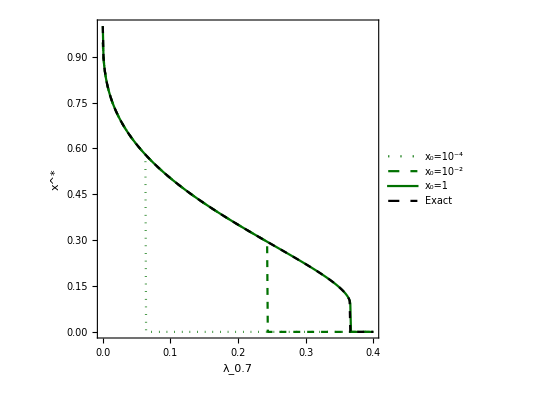

```mathematica
ListPlot[

x0 list,
Joined->True,
Frame->True,
AspectRatio->1,
PlotStyle->{{Green//Darker//Darker,Dotted},{Green//Darker//Darker,Dashed},{Green//Darker//Darker},{Dashed,Black}},

PlotLegends->Placed[{"x_0=10^-4","x_0=10^-2","x_0=1","Exact"},{Right,Top}],

FrameLabel->{"λ_0.7","x^*"},
FrameStyle->14
]
```

```mathematica
GD log[x0_,p_]:=ParallelTable[
X={x0};
For[i=1,i<200,i++,
AppendTo[X,update[X[[-1]],λ,0.8,p,4]//Chop]
];
{λ,X[[-1]]},
{λ,0,1,0.001}];

λc x0 list=Table[{x0,Select[GD log[x0,0.7],#[[2]]==0&][[1,1]]},{x0,PowerRange[10.^-5,1,10^(5/50)]}];
fit[x_]=10^Fit[Select[λc x0 list,#[[1]]<10^-2&]//Log10,{1,x},x]/.x->Log10[x];
```

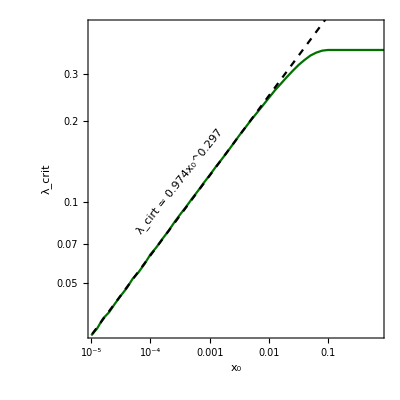

```mathematica
base=fit[1];
pow=D[Log[fit[x]/fit[1]],x]/.x->1;
formattedExpression=ToString[NumberForm[base,{∞,3}]]<>"\!\(\*SubsuperscriptBox[\(x\), \(0\), \("<>ToString[NumberForm[pow,{∞,3}]]<>"\)]\)";

Show[
ListLogLogPlot[λc x0 list,PlotStyle->{{Green//Darker//Darker}},Joined->True],
LogLogPlot[fit[x],{x,10^-8,1},PlotStyle->{{Black,Dashed}}],

Frame->True,
AspectRatio->1,
PlotRange->{{Log[1.1 10^-5],Log[0.7]},{Log[0.033],Log[0.45]}},
FrameStyle->14,
FrameLabel->{"x_0","λ_crit"},
Epilog->{
Inset[Style[Rotate["λ_cirt ≃ "<>formattedExpression,π/3.5]],{Log[10^-3.5],Log[.12]}]
},

Background->White

]
```

```mathematica
D[Log[fit[x]/fit[1]],x]/.x->1
```

```mathematica
fit[x]
```

0.973995 x^0.296514

0.297

```mathematica
"x_0^0.34"
```